```mathematica
nbdir=ToString[NotebookDirectory[]]
```

/home/mls/Code/multimode/

```mathematica
dir1=nbdir<>"fP=100_Delta0=50_N=1000_zA=0_epsilon=0_E0=50_64-grid_K-kerns_grid-factor";
SetDirectory[dir1]
filename=FileNames["*h5"][[1]];
t1 = Import[filename, {"Datasets", "/1/t"}];
x1 = Import[filename, {"Datasets", "/1/x"}];
y1 = Import[filename, {"Datasets", "/1/y"}];
imatom1 = Import[filename, {"Datasets", "/1/imatom"}];
reatom1 = Import[filename, {"Datasets", "/1/reatom"}];
imlight1 = Import[filename, {"Datasets", "/1/imlight"}];
relight1 = Import[filename, {"Datasets", "/1/relight"}];
modatomsq1 = Import[filename, {"Datasets", "/1/modatom"}];
modlightsq1= Import[filename, {"Datasets", "/1/modlight"}];
relightint1 = Import[filename, {"Datasets", "/1/relightint"}];
imlightint1 = Import[filename, {"Datasets", "/1/imlightint"}];
ResetDirectory[];
```

/home/mls/Code/multimode/fP=100_Delta0=50_N=1000_zA=0_epsilon=0_E0=50_64-grid_K-kerns_grid-factor

```mathematica
dir2=nbdir<>"fP=100_Delta0=50_N=1000_zA=0_epsilon=0_E0=50_96-grid_K-kerns_grid-factor";
SetDirectory[dir2]
filename=FileNames["*h5"][[1]];
t2 = Import[filename, {"Datasets", "/1/t"}];
x2 = Import[filename, {"Datasets", "/1/x"}];
y2 = Import[filename, {"Datasets", "/1/y"}];
imatom2 = Import[filename, {"Datasets", "/1/imatom"}];
reatom2 = Import[filename, {"Datasets", "/1/reatom"}];
imlight2 = Import[filename, {"Datasets", "/1/imlight"}];
relight2 = Import[filename, {"Datasets", "/1/relight"}];
modatomsq2 = Import[filename, {"Datasets", "/1/modatom"}];
modlightsq2= Import[filename, {"Datasets", "/1/modlight"}];
relightint2 = Import[filename, {"Datasets", "/1/relightint"}];
imlightint2 = Import[filename, {"Datasets", "/1/imlightint"}];
ResetDirectory[];
```

/home/mls/Code/multimode/fP=100_Delta0=50_N=1000_zA=0_epsilon=0_E0=50_96-grid_K-kerns_grid-factor

```mathematica
dir3=nbdir<>"fP=100_Delta0=50_N=1000_zA=0_epsilon=0_E0=50_128-grid_K-kerns_grid-factor";
SetDirectory[dir3]
filename=FileNames["*h5"][[1]];
t3 = Import[filename, {"Datasets", "/1/t"}];
x3 = Import[filename, {"Datasets", "/1/x"}];
y3 = Import[filename, {"Datasets", "/1/y"}];
imatom3 = Import[filename, {"Datasets", "/1/imatom"}];
reatom3 = Import[filename, {"Datasets", "/1/reatom"}];
imlight3 = Import[filename, {"Datasets", "/1/imlight"}];
relight3 = Import[filename, {"Datasets", "/1/relight"}];
modatomsq3 = Import[filename, {"Datasets", "/1/modatom"}];
modlightsq3= Import[filename, {"Datasets", "/1/modlight"}];
relightint3= Import[filename, {"Datasets", "/1/relightint"}];
imlightint3 = Import[filename, {"Datasets", "/1/imlightint"}];
ResetDirectory[];
```

/home/mls/Code/multimode/fP=100_Delta0=50_N=1000_zA=0_epsilon=0_E0=50_128-grid_K-kerns_grid-factor

```mathematica
(* Declare variables, max variables *)
```

```mathematica
tmax=Length[t1]
ymax1=Length[y1];
xmax1=Length[x1]
xmid1=xmax1/2+1
{First[x1], Last[x1]}
```

501

64

33

{-12.,11.625}

```mathematica
tmax2=Length[t2]
ymax2=Length[y2];
xmax2=Length[x2]
xmid2=xmax2/2+1
{First[x2], Last[x2]}
```

501

96

49

{-12.,11.75}

```mathematica
tmax3=Length[t3]
ymax3=Length[y3];
xmax3=Length[x3]
xmid3=xmax3/2+1
{First[x3], Last[x3]}
```

501

128

65

{-12.,11.8125}

```mathematica
(* Abs atomic field density plot *)
```

```mathematica
tmax==tmax2==tmax3
```

True

```mathematica
plotmax=tmax;
plotint=20;
```

## 1D plots

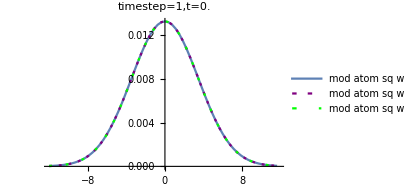
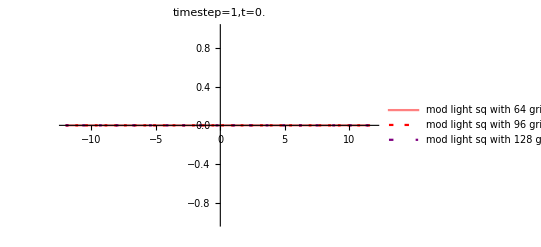
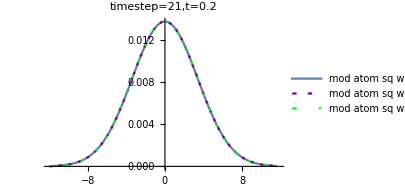
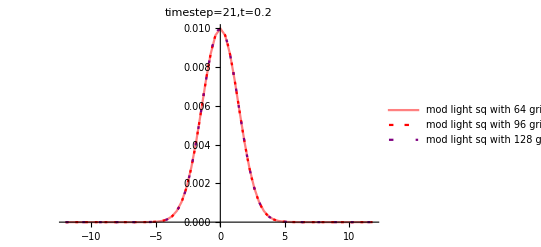
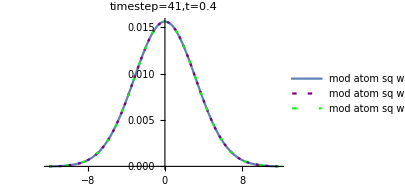
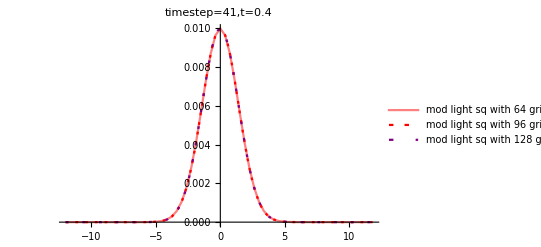
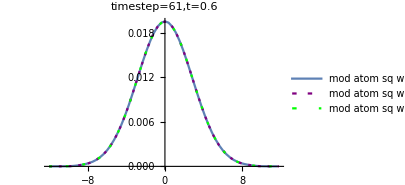
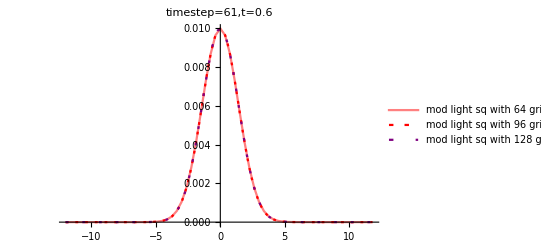

```mathematica
(* Abs val of atomic and light field by time step *)
Table[{ListLinePlot[{Table[{ x1[[i]] ,modatomsq1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]] ,modatomsq2[[t,i,xmid2]]} ,{i,1,xmax2}],Table[{ x3[[i]] ,modatomsq3[[t,i,xmid3]]} ,{i,1,xmax3}]},ImageSize->300,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotLegends->Placed[{"mod atom sq with 64 gridpoints","mod atom sq with 96 gridpoints","mod atom sq with 128 gridpoints"},Below],PlotStyle->{Thick,{Purple,Thick,AbsoluteDashing[{2,5}]},{Green,Thick,AbsoluteDashing[{2,10}]}},PlotRange->All],ListLinePlot[{Table[{ x1[[i]],modlightsq1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]],modlightsq2[[ t,i,xmid2]]} ,{i,1,xmax2}],Table[{ x3[[i]] ,modlightsq3[[t,i,xmid3]]} ,{i,1,xmax3}]},ImageSize->400,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotStyle->{{Pink,Thick},{Red,Thick,AbsoluteDashing[{2,5}]},{Purple,Thick,AbsoluteDashing[{2,10}]}},PlotLegends->Placed[{"mod light sq with 64 gridpoints","mod light sq with 96 gridpoints","mod light sq with 128 gridpoints"},Below],PlotRange->All]},{t,1,plotmax,plotint}]
```

```mathematica
(* Real part of atomic and light field by time step *)
```

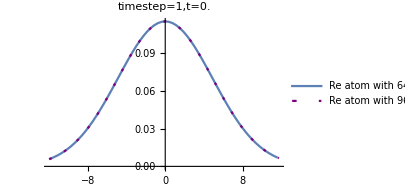
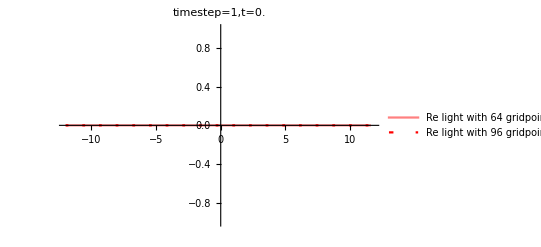
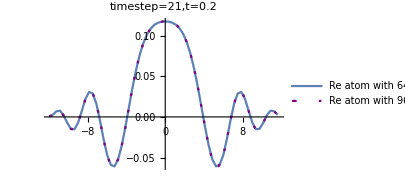
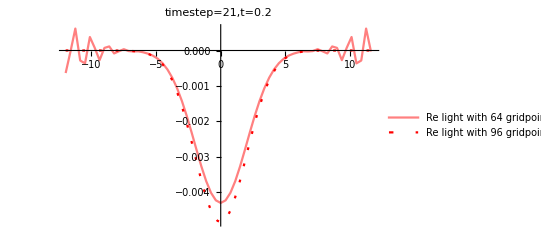
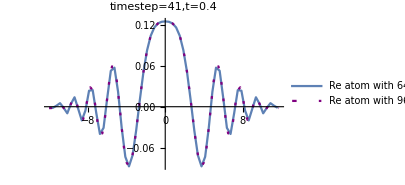
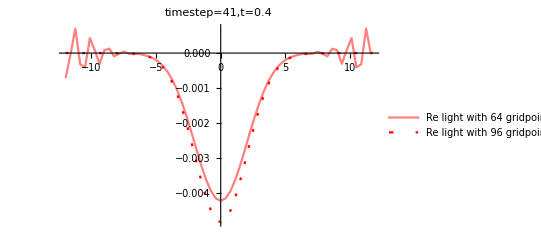
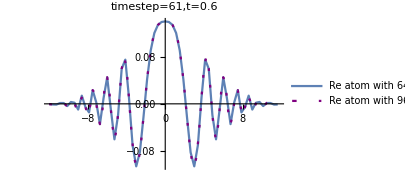
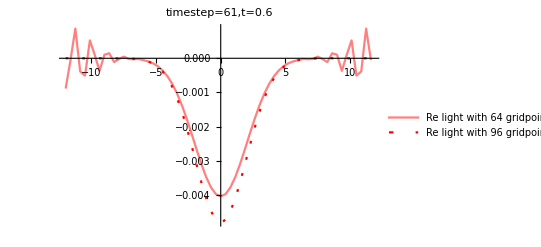

```mathematica
Table[{ListLinePlot[{Table[{ x1[[i]] ,reatom1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]] ,reatom2[[t,i,xmid2]]} ,{i,1,xmax2}]},ImageSize->300,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotLegends->Placed[{"Re atom with 64 gridpoints","Re atom with 96 gridpoints"},Below],PlotStyle->{Thick,{Purple,Thick,AbsoluteDashing[{2,10}]}},PlotRange->All],ListLinePlot[{Table[{ x1[[i]],relight1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]],relight2[[t,i,xmid2]]} ,{i,1,xmax2}]},ImageSize->400,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotStyle->{{Pink,Thick},{Red,Thick,AbsoluteDashing[{2,10}]}},PlotLegends->Placed[{"Re light with 64 gridpoints","Re light with 96 gridpoints"},Below],PlotRange->All]},{t,1,plotmax,plotint}]
```

```mathematica
(* Im part of atomic and light field by time step *)
```

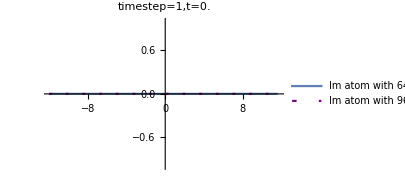
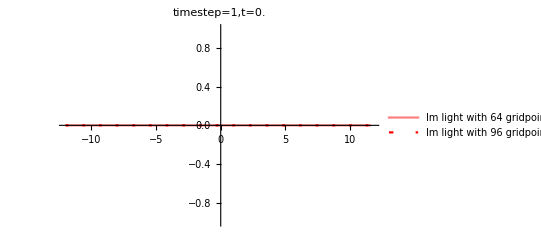
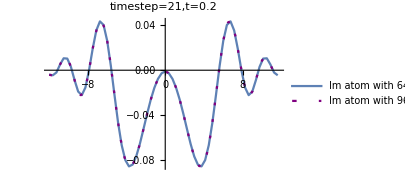
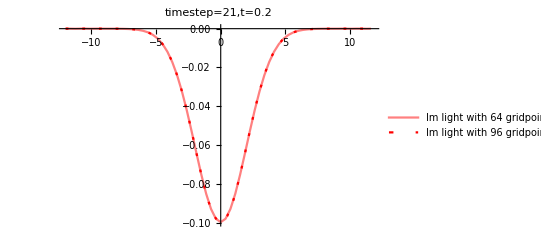
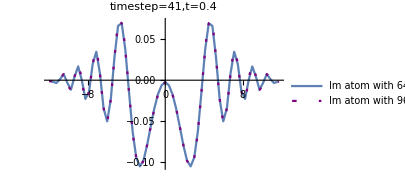
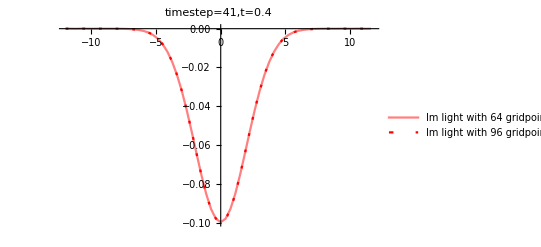
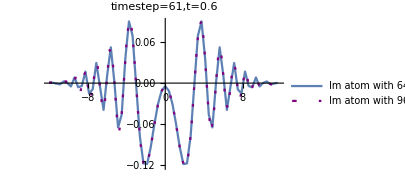
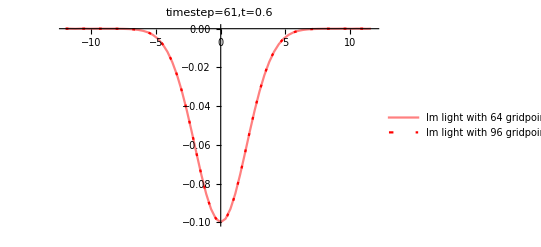
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Table[{ListLinePlot[{Table[{ x1[[i]] ,imatom1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]] ,imatom2[[t,i,xmid2]]} ,{i,1,xmax2}]},ImageSize->300,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotLegends->Placed[{"Im atom with 64 gridpoints","Im atom with 96 gridpoints"},Below],PlotStyle->{Thick,{Purple,Thick,AbsoluteDashing[{2,10}]}},PlotRange->All],ListLinePlot[{Table[{ x1[[i]],imlight1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]],imlight2[[t,i,xmid2]]} ,{i,1,xmax2}]},ImageSize->400,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotStyle->{{Pink,Thick},{Red,Thick,AbsoluteDashing[{2,10}]}},PlotLegends->Placed[{"Im light with 64 gridpoints","Im light with 96 gridpoints"},Below],PlotRange->All]},{t,1,plotmax,plotint}]
```

```mathematica
(* Light int by time step *)
```

```mathematica
Table[{ListLinePlot[{Table[{ x1[[i]] ,relightint1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]] ,relightint2[[t,i,xmid2]]} ,{i,1,xmax2}],Table[{ x3[[i]] ,relightint3[[t,i,xmid3]]} ,{i,1,xmax3}]},ImageSize->300,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotLegends->Placed[{"Im atom with 64 gridpoints","Im atom with 96 gridpoints","Im light with 128 gridpoints"},Below],PlotStyle->{Thick,{Purple,Thick,AbsoluteDashing[{2,5}]},{Green,Thick,AbsoluteDashing[{2,10}]}},PlotRange->All],ListLinePlot[{Table[{ x1[[i]],imlightint1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]],imlightint2[[t,i,xmid2]]} ,{i,1,xmax2}],Table[{ x3[[i]] ,imlightint3[[t,i,xmid3]]} ,{i,1,xmax3}]},ImageSize->400,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotStyle->{{Pink,Thick},{Red,Thick,AbsoluteDashing[{2,5}]},{Purple,Thick,AbsoluteDashing[{2,10}]}},PlotLegends->Placed[{"Im light with 64 gridpoints","Im light with 96 gridpoints","Im light with 128 gridpoints"},Below],PlotRange->All]},{t,1,plotmax,plotint}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

## 2D graphs

```mathematica
(*Table[{ListDensityPlot[Flatten[Table[{ x1[[i]] ,y1[[j]],modatomsq1[[t,i,j]]} ,{i,1,xmax1},{j,1,ymax1}],1],ImageSize->300,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotRange->All],ListDensityPlot[Flatten[Table[{ x2[[i]] ,y2[[j]],modatomsq2[[t,i,j]]} ,{i,1,xmax2},{j,1,ymax2}],1],ImageSize->300,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotRange->All,ColorFunction->"BlueGreenYellow"]},{t,1,plotmax,plotint}]*)
```